#### Lecture: replacements and trees

Basic examples.
Basically,

```mathematica
x/.x->y
```

y

The x -> y part is called “rule”, /. is a shortcut for the command ReplaceAll[expression, rules].

```mathematica
ReplaceAll[x,x->y]
```

y

You can do it in complicated expressions.

```mathematica
√x BesselK[x^2/2,1]+x Sin[x]/.x->y
```

√y BesselK[y^2/2,1]+y Sin[y]

Or with functions.

```mathematica
√x BesselK[x^2/2,1]+x Sin[x]/.Sin->Cos
```

√x BesselK[x^2/2,1]+x Cos[x]

Or with patterns (meaning, “everything that looks like...”)

```mathematica
(Sin[x/2]Sinh[y])/(Sin[x/2]Cosh[y]+Cos[x/2]Sinh[y])/.Sin[p_]->Sin[2p]
```

(Sin[x] Sinh[y])/(Cosh[y] Sin[x]+Cos[x/2] Sinh[y])

By the way, it’s convenient to correct mistakes. It is similar to “Find all -> Replace with” structure.
You can use more than one replacement in one “/.”

```mathematica
(Sin[x/2]Sinh[y])/(Sin[x/2]Cosh[y]+Cos[x/2]Sinh[y])/.{Sin[p_]->Sin[2p],Cos[p_]->Cos[2p]}
```

(Sin[x] Sinh[y])/(Cosh[y] Sin[x]+Cos[x] Sinh[y])

Also, you can use an array of replacements.

```mathematica
x/.{{x->3},{x->4},{x->5}}
```

{3,4,5}

Primary usage of that feature looks like this:

```mathematica
x/.Solve[x^2+1==0,x]
```

{-ⅈ,ⅈ}

Solve and many other “solving” functions return sets of rules. We’ll talk about it later.
Let’s complete some exercises together, just to remember syntax.

```mathematica
x+y/.{x->2,y->1}
```

```mathematica
x+y/.{{x->y},{x->1,x->2,y->3}}
```

Last example is quite straightforward: rules are processed from left to right, so x is changed to 1, not to 2.

Now, let’s talk about problems. Consider the following.

```mathematica
2x/.{x->a,2x->b}
```

b

This result may seem counterintuitive. Going from left to right, we should change x to a and get 2a, with the second rule having no effect, right?.. Obviously, wrong. To understand, why, we need to look at expression from the Mathematica point of view.

## Expression trees

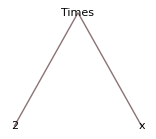

```mathematica
2x//TreeForm
```

That structure is known as “expression tree”. It’s exactly what it says on the label - the tree representation of expression. Expressions as humans write them are nontrivial. They contain brackets, the order of evaluating operators is not linear (2+2*2), operators and variables are everywhere... Mess. On the other hand, trees are quite convenient for machines. I won’t go into the advantages here, you can always read about it or just write some simple calculator.
The root of the tree is an operation you will compute LAST. Operators have children: the numbers they are acting at, and “number” can be another operator.Consequently,one should evaluate such a tree from the leaves up to the root; programmatically, one will have a recursive function “evaluate”, which will be applied to the root and will call itself whenever child of the operator is operator itself.

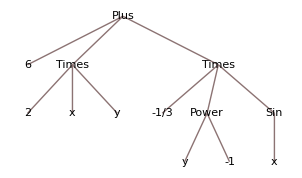

```mathematica
2x y + 6-Sin[x]/(3 y)//TreeForm
```

Important notes to self: Plus and Times can have many arguments; division is represented as taking minus first power of whatever; minus is represented as Plus (Times -1).

Some examples here; any expression can be expanded into tree, do it.

Mathematica applies (something like) the algorithm below to the root of the tree.
1) Take the element of the tree. Check rules, left to right, to see if there’s one that coincides with some subtree of the tree that grows from that element. 
1.1) If found:
	2) stop checking 
	3) make replacement 
	4) apply 1) to anything that goes down from the replaced part.
1.2) If not found:
	5) apply 1) to every child of the root

And now we need many, many examples.

```mathematica
2x/.{x->a,2x->b}
```

b

The root element is Times, it has to children, 2 and x. Checking x: x is not Times, continue. Checking Times-2-x: it coincides with the tree, apply rule 2x -> b.

```mathematica
Sin[Sin[x]]/.Sin->Cos
```

Cos[Cos[x]]

The root element is Sin; checking the only rule, applying it. Then, continue to the children of changed expression. There’ll be one more Sin, rule applied, and x, nothing done.

```mathematica
2 Sin[x]/. 2 Sin->Cos
```

2 Sin[x]

Not an easy one. 2 has no children, Sin has child x, so it’s impossible to understand how many child should Cos from the rule have. In that case, nothing is done.

```mathematica
Sin[x]Cos[x]/.Sin Cos->Tan
```

Cos[x] Sin[x]

x may seem the same in Sin and Cos, but it’s two different leaves in the tree, so that case is similar to the previous. You could do it with

```mathematica
(2Sin)[x]/. 2Sin->Cos
```

Cos[x]

But that’s absolutely useless, since one operator (2 Sin) is not Sin doubled. Mathematica doesn’t know what to do with it.

```mathematica
(2Sin)[5]//N
```

(2. Sin)[5.]

Now, there was recursion in the algorithms. Let’s consider one of the “basic examples”

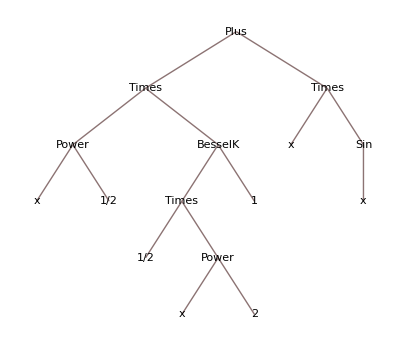

```mathematica
√x BesselK[x^2/2,1]+x Sin[x]//TreeForm
```

```mathematica
√x BesselK[x^2/2,1]+x Sin[x]/.x->y
```

√y BesselK[y^2/2,1]+y Sin[y]

Is Plus equal to x? No. Check it’s children. Is either of Times equal to x? No. Check their children. Their we can see Sin, Power, BesselK and x. Apply rule to x and check all the children of operators. That way it will go down to all the leaves, changing every x to y.

Now, there was some talk about the subtrees. The reason is that some operators don’t have definite number of arguments. Consider Plus.

```mathematica
3+x+y/. 3+x->a
```

a+y

Despite the fact that Plus of 3+x+y has three children, and Plus of 3+x - only two, the rule is applied, and the subtree that matched to the lhs of the rule was changed. Complication with this approach is that Mathematica doesn’t try to apply the rule to the children which were NOT changed. I mean,

```mathematica
3+x+Sin[3+x]/. 3+x->a
```

a+Sin[3+x]

As you can see, the second 3+x wasn’t changed just because the operator it connected to was partially changed. I think that it’s wrong approach, but I don’t write the rules.
You can overcome this obstacle by using ReplaceRepeated, or //.

```mathematica
3+x+Sin[3+x]//. 3+x->a
```

a+Sin[a]

```mathematica
ReplaceRepeated[3+x+Sin[3+x], 3+x->a]
```

a+Sin[a]

Living up to it’s name, ReplaceRepeated process the whole tree, and if it has applied the rule at least once, it returns to the root of the tree and starts again. Yeah, I know, everyone wants to see StackOverflow.

```mathematica
x//.{x->y,y->x}
```

ReplaceRepeated::rrlim: Exiting after x scanned 65536 times.

x

That should be every creepy feature of ReplaceAll. Anyway, it’s everything I was able to find, and I’m pretty good at finding creepy features.
Since there’re ReplaceAll and ReplaceRepeated, it seems possible there’s just Replace. Unfortunately, there’s. No shortcut for that one, it’s way too TreeForm-dependent to be frequently used.

```mathematica
Replace[x,x->a]
```

a

```mathematica
Replace[1+x,x->a]
```

1+x

Replace in the basic form only tries to apply rules to the root of the tree.
But it has third argument, called levelspec in docs. Rules will be applied to the level of the tree number levelspec, the third argument. The root has level 0.

```mathematica
Replace[1+x,x->a,1]
```

1+a

```mathematica
Replace[1+x,x->a,0]
```

1+x

It has it’s uses, but first we need to talk about patterns and conditions.

## Patterns and conditions.

Before, I said that a pattern is “anything”. Now I would like to say “any subtree”. Or even “maximal subtree”, since Mathematica will always try to find maximal subtree. Entering p_, you allow Mathematica to put any subtree in place of p. She will use that allowance quite freely.

```mathematica
√x BesselK[x^2/2,1]+x Sin[x]/.x_->a
```

a

Yeah. Mathematica starts from the root and seeks for subtree... Whole tree is a perfect candidate. So the whole expression just became x and was changed to a.
In basic examples there’s a good example of using patterns by themselves.

```mathematica
(Sin[x/2]Sinh[y])/(Sin[x/3]Cosh[y]+Cos[x/2]Sinh[y])/.{Sin[p_]->Sin[2p],Cos[p_]->Cos[2p]}
```

(Sin[x] Sinh[y])/(Cosh[y] Sin[(2 x)/3]+Cos[x] Sinh[y])

Multiply all arguments of trigonometric functions by two? Easy. Here, Mathematica seeks a node with Sin or Cos and names p the subtree that grows from such node. Makes sense.

But patterns have one more convenient feature. Conditions.

```mathematica
{1, 123,-24,14,5}/.x_/;OddQ[x]->0
```

{0,0,-24,14,0}

/;, aka Condition, is a condition on a pattern. Rule is applied only if condition is satisfied. In the example above I changed every odd quantity to zero. I could also use many logical expressions

```mathematica
{1, 123,-24,14,5}/.x_/;OddQ[x]||x>0->0
```

{0,0,-24,0,0}

A little more useful usage - setting every symbolic quantity to zero. Function NumericQ (numeric quantity) checks whether its argument is a number, so...

```mathematica
2π+x^2+25 owl^37+y^3/.x_/;Not[NumericQ[x]]->0
```

0

Oh, wait. I wanted 2π. But since Mathematica firstly used the whole expression as x, and it’s not numeric, it all became zero...
For polynomials, one can use

```mathematica
Replace[2π+x^2+25 owl^37+y^3,x_/;Not[NumericQ[x]]->0,1]
```

2 π

Replace only uses rule on the first level of the tree, on each of the addends. Hence you got the only term that’s numeric quantity.
Doing it in general case is... interesting exercise.
The same way you can cut the series, or leave out odd powers.

```mathematica
1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800/.x^n_/;n>4->0
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800/.x^n_/;EvenQ[n]->0
```

1+x+x^3/6+x^5/120+x^7/5040+x^9/362880

(OddQ won’t work as expected, though. Why?)

## Some fun, some usage

I really hope that I gave you either a strong understanding of replacements, or as strong a motivation to not use them in your workflow. First is cool, second is Ok, at least you won’t be stuck debugging some complicated undebuggable replacement.

I usually use them for symbolic -> numeric conversion.

```mathematica
(Sin[x/2]Sinh[y])/(Sin[x/3]Cosh[y]+Cos[x/2]Sinh[y])/.{x->Pi,y->Pi/2}//N
```

1.05904

I’m too lazy to define functions, replacements work just fine in such setting.

As I already mentioned, everything solving returns results in form of replacements. Unexpectedly, sometimes it’s really convenient. The following is easier than Map usage.

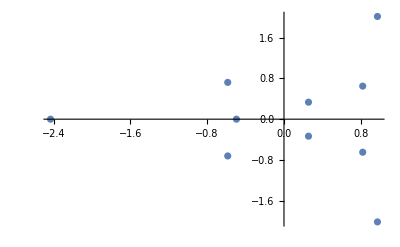

```mathematica
ListPlot[{Re[x],Im[x]}/.Solve[x^10+12 x^7-5 x^6+11 x^3-x+1==0,x]]
```

A-and... Replacements can do quite powerful things. Two rules all in all to transform any logarithmic expression into expanded form. Or into one Log.

```mathematica
logExpandRules={Log[x_ y_]->Log[x]+Log[y],Log[x_^y_]->y Log[x]};
Log[5 x^2]+Log[10 x y^(-1/2)]//.logExpandRules
```

Log[5]+Log[10]+3 Log[x]-Log[y]/2

```mathematica
logFactorRules={Log[x_]+Log[y_]->Log[x y],y_ Log[x_]->Log[x^y]};
Log[5 x^2]+2Log[10 x y^(-1/2)]//.logFactorRules
```

Log[(500 x^4)/y]

What about trigonometric functions? At least with function of sums?